# Statistics for area and perimeter

### data loading

```mathematica
p0s={3.85,3.825,3.80};
```

```mathematica
temperatures={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{2, 4,10, 20, 40,60, 80, 200, 500, 800, 1400, 2500, 4200,5000, 6000, 8500, 9500},{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000},{1, 3, 4 ,8 ,15,40 ,70 ,150 ,250, 600 ,2000, 2500 ,4500,9500}};
```

```mathematica
areaPerimeters=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/areaPeri_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
thirdCum=Table[Table[CentralMoment[Flatten[Table[Flatten[Normal[areaPerimeters[[p,T,i,2]]]]-p0s[[p]],{i,Length[areaPerimeters[[p,T]]]}]],3],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{-0.0000339703,-6.32769×10^-6,-3.76715×10^-7,-9.73279×10^-8,-3.171×10^-7,4.47074×10^-8,6.67305×10^-8,3.29765×10^-8,1.71673×10^-8,2.43549×10^-9,-4.70969×10^-9,-5.88684×10^-9,4.45313×10^-10,-1.00112×10^-9,-9.00749×10^-11,2.94318×10^-10,6.30195×10^-11},{-0.000110444,-0.000038317,-0.0000262184,-6.15057×10^-6,-3.06188×10^-6,-1.4607×10^-7,-2.8689×10^-7,2.54386×10^-7,6.82793×10^-8,-6.78885×10^-8,2.30241×10^-7,2.19993×10^-7,1.70886×10^-7,4.10355×10^-8,3.28848×10^-8,1.20212×10^-8},{-0.000104696,-0.0000344459,-0.0000236454,-0.0000174853,-5.90796×10^-6,-3.78283×10^-7,-1.2088×10^-6,-4.43871×10^-7,4.89341×10^-8,-1.98271×10^-7,2.50028×10^-7,-3.75948×10^-8,3.05402×10^-7,-4.81262×10^-8}}

```mathematica
fourthCum=Table[Table[CentralMoment[Flatten[Table[Flatten[Normal[areaPerimeters[[p,T,i,2]]]]-p0s[[p]],{i,Length[areaPerimeters[[p,T]]]}]],4],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.000513687,0.0000991498,0.0000413738,0.0000113644,7.04182×10^-6,3.1672×10^-6,2.09434×10^-6,5.83838×10^-7,1.58776×10^-7,7.31064×10^-8,4.27191×10^-8,1.38304×10^-8,6.01283×10^-9,4.27178×10^-9,2.11914×10^-9,1.48984×10^-9,9.57902×10^-10},{0.00125032,0.000510068,0.000333482,0.0000967503,0.0000402381,0.0000264263,0.0000168849,0.0000110847,6.75135×10^-6,4.56268×10^-6,3.07248×10^-6,2.02518×10^-6,1.18746×10^-6,5.56835×10^-7,2.68026×10^-7,1.54885×10^-7},{0.00123508,0.000500631,0.000327367,0.000221211,0.0000953661,0.0000393477,0.0000256096,0.0000163497,0.0000106793,6.52473×10^-6,4.35711×10^-6,3.60065×10^-6,2.8754×10^-6,2.30129×10^-6}}

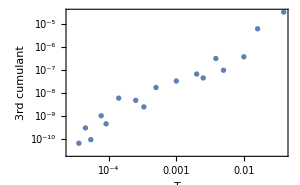
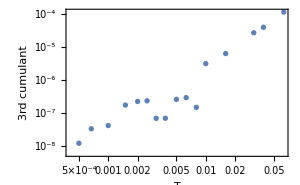
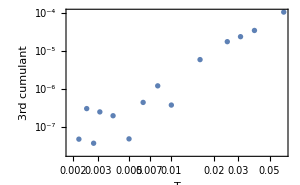

```mathematica
Table[ListLogLogPlot[Table[{temperatures[[p,T]],Abs[thirdCum[[p,T]]]},{T,Length[temperatures[[p]]]}],ImageSize->300,FrameLabel->{"T","3rd cumulant"}],{p,Length[p0s]}]
```

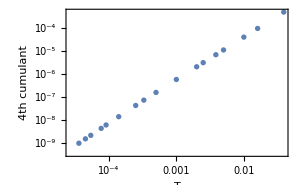
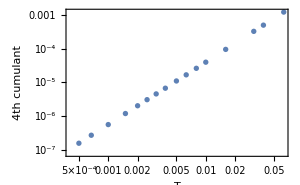
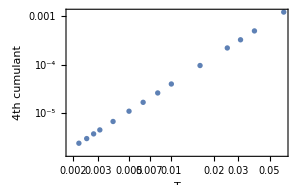

```mathematica
Table[ListLogLogPlot[Table[{temperatures[[p,T]],Abs[fourthCum[[p,T]]]},{T,Length[temperatures[[p]]]}],ImageSize->300,FrameLabel->{"T","4th cumulant"}],{p,Length[p0s]}]
```

### pdf of p and q

```mathematica
SetOptions[SmoothHistogram,defaultPlotOptions]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→Directive[GrayLevel[0],Thickness[0.002]],FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{GrayLevel[0],FontFamily→Arial,FontSize→16},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotHighlighting→Automatic,PlotLabel→None,PlotLabels→None,PlotLayout→Automatic,PlotLegends→None,PlotPoints→Automatic,PlotRange→All,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

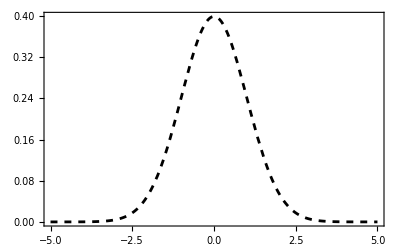

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-5,5},PlotStyle->{Dashed,Black}]
```

```mathematica
|
```

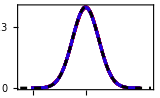

```mathematica
pdfp=Show[Flatten[Table[SmoothHistogram[Table[(Flatten[Table[Flatten[Normal[areaPerimeters[[p,T,i,2]]]],{i,Length[areaPerimeters[[p,T]]]}]]-Mean[Flatten[Table[Flatten[Normal[areaPerimeters[[p,T,i,2]]]],{i,Length[areaPerimeters[[p,T]]]}]]])/Sqrt[Variance[Flatten[Table[Flatten[Normal[areaPerimeters[[p,T,i,2]]]],{i,Length[areaPerimeters[[p,T]]]}]]]],{T,Length[temperatures[[p]]]}],ImageSize->160,LabelStyle->Directive[FontSize->24,FontName->"Arial"],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameTicks->{{{{0,0,0.05},{0.1,0.1,0.05},{0.2,0.2,0.05},{0.3,0.3,0.05},{0.4,0.4,0.05}},None},{{{0,0,0.06},{2,None,0.04},{4,4,0.06},{-2,None,0.04},{-4,-4,0.06}},None}}],{p,Length[p0s]}]],Plot[PDF[NormalDistribution[0,1],x],{x,-5,5},PlotStyle->{Dashed,Black}]]
```

```mathematica
qqp=Table[QuantilePlot[Table[Flatten[Table[Flatten[Normal[areaPerimeters[[p,T,i,2]]]]-p0s[[p]],{i,Length[areaPerimeters[[p,T]]]}]],{T,Length[temperatures[[p]]]}],ImageSize->400,PlotLabel->"Quantile plot: p-p0 for p0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]]],{p,Length[p0s]}]
```

```mathematica
Export["/home/chengling/Research/updates/11102024/distributionp.jpeg",Grid[Partition[Flatten[Table[{pdfp[[i]],qqp[[i]]},{i,3}]],2]],ImageResolution->300]
```

/home/chengling/Research/updates/11102024/distributionp.jpeg

```mathematica
QuantilePlot[Flatten[Table[Flatten[Normal[areaPerimeters[[3,1,i,2]]]]-3.85,{i,Length[areaPerimeters[[3,1]]]}]],NormalDistribution[0,1]]
```

-Graphics-

```mathematica
pdfq=Table[SmoothHistogram[Table[Flatten[Table[Flatten[Normal[areaPerimeters[[p,T,i,2]]]]/Flatten[Normal[areaPerimeters[[p,T,i,1]]]]-p0s[[p]],{i,Length[areaPerimeters[[p,T]]]}]],{T,Length[temperatures[[p]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],PlotLabel->"PDF of q-p0 for p0="<>ToString[p0s[[p]]]],{p,Length[p0s]}]
```

```mathematica
qqq=Table[QuantilePlot[Table[Flatten[Table[Flatten[Normal[areaPerimeters[[p,T,i,2]]]]/Flatten[Normal[areaPerimeters[[p,T,i,1]]]]-p0s[[p]],{i,Length[areaPerimeters[[p,T]]]}]],{T,Length[temperatures[[p]]]}],ImageSize->400,PlotLabel->"Quantile plot q-p0 for p0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]]],{p,Length[p0s]}]
```

```mathematica
Export["/home/chengling/Research/updates/11102024/distributionq.jpeg",Grid[Partition[Flatten[Table[{pdfq[[i]],qqq[[i]]},{i,3}]],2]],ImageResolution->300]
```

/home/chengling/Research/updates/11102024/distributionq.jpeg

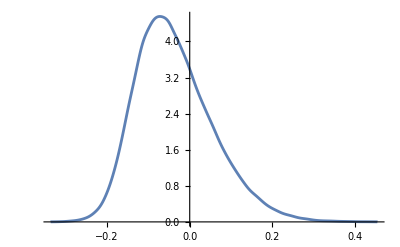

```mathematica
SmoothHistogram[Flatten[Table[Flatten[Normal[areaPerimeters[[3,10,i,2]]]]/Flatten[Normal[areaPerimeters[[3,10,i,1]]]]-3.85,{i,Length[areaPerimeters[[3,10]]]}]]]
```

```mathematica
meanPminusp0=Table[Table[Mean[Flatten[Table[Flatten[Normal[areaPerimeters[[p,T,i,2]]]-p0s[[p]]],{i,Length[records[[p]]]}]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.0558539,0.0284207,0.0188158,0.00924418,0.00684278,0.00400836,0.00286971,0.00103357,0.000414153,0.000248805,0.000128403,0.000107193,0.0000570874,0.000066725,0.0000348535,0.0000183148,0.0000249634},{0.0871826,0.0673969,0.0585367,0.0368247,0.0250869,0.0204769,0.0164134,0.0128776,0.00956604,0.00747848,0.00566521,0.00418469,0.00273761,0.00137834,0.000406726,0.0000214017},{0.101896,0.0793375,0.0703126,0.0614995,0.046053,0.0321453,0.0260206,0.0205137,0.0158122,0.0112847,0.00783352,0.00641558,0.00531642,0.00415221}}

```mathematica
{1,1,3}/{5,7,8}
```

{1/5,1/7,3/8}

```mathematica
meanQminusq0=Table[Table[Mean[Flatten[Table[Flatten[Normal[areaPerimeters[[p,T,i,2]]]/Normal[areaPerimeters[[p,T,i,1]]]-p0s[[p]]],{i,Length[records[[p]]]}]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.0738145,0.0375819,0.0253742,0.0133434,0.0102948,0.00660645,0.0050946,0.00238168,0.00119783,0.00079469,0.000557042,0.000357658,0.000224546,0.000209727,0.000136053,0.000102695,0.0000929687},{0.112573,0.084536,0.0727996,0.0453039,0.0310583,0.0255509,0.020721,0.0165558,0.01263,0.0101426,0.00796413,0.00615304,0.00435699,0.00258899,0.00129432,0.000723982},{0.126424,0.0956184,0.0837999,0.0727837,0.0538639,0.0375186,0.0305341,0.0242623,0.0189164,0.0138053,0.00989529,0.00829904,0.00703312,0.00569235}}

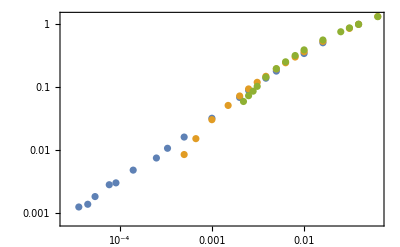

```mathematica
ListLogLogPlot[Table[Table[{temperatures[[p,T]],meanQminusq0[[p,T]]/meanQminusq0[[p,{1,2,2}[[p]]]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]]
```

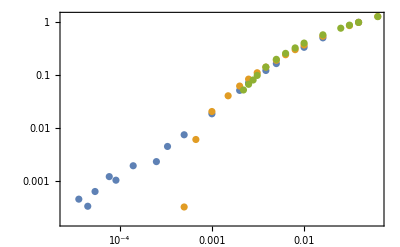

```mathematica
ListLogLogPlot[Table[Table[{temperatures[[p,T]],meanPminusp0[[p,T]]/meanPminusp0[[p,{1,2,2}[[p]]]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]]
```

## tension

```mathematica
openHexagon=Graphics[{EdgeForm[{Blue,Thickness[0.03]}],FaceForm[None],Polygon[Table[{Cos[θ],Sin[θ]},{θ,0,2 π,π/3}]]},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,Background->Transparent,ImageSize->20]
```

-Graphics-

```mathematica
blueGraient=Flatten[Table[{RGBColor[0.5,0.7,1,0.6],RGBColor[0.3,0.5,0.8,0.6],RGBColor[0,0.1,0.5,0.6]},{i,4}]]
```

{RGBColor[0.5, 0.7, 1, 0.6],RGBColor[0.3, 0.5, 0.8, 0.6],RGBColor[0, 0.1, 0.5, 0.6],RGBColor[0.5, 0.7, 1, 0.6],RGBColor[0.3, 0.5, 0.8, 0.6],RGBColor[0, 0.1, 0.5, 0.6],RGBColor[0.5, 0.7, 1, 0.6],RGBColor[0.3, 0.5, 0.8, 0.6],RGBColor[0, 0.1, 0.5, 0.6],RGBColor[0.5, 0.7, 1, 0.6],RGBColor[0.3, 0.5, 0.8, 0.6],RGBColor[0, 0.1, 0.5, 0.6]}

```mathematica
tension={{0.2422332868686113,0.12304777927124538,0.08087674266563366,0.039941897094602816,0.029826242469666343,0.01782752952655755,0.013481243374732322,0.005499136581105852,0.002223255946361173,0.0013392654052048108,0.0009871610106626824,0.0005192269692388164,0.0003246548658641914,0.00027961123994239633,0.0002039728875604251,0.0001629184313958167,0.00013270379977750913},{0.3805639982577122,0.286482996829732,0.24739465802357644,0.15379208490116492,0.10430139326631785,0.08520280674196938,0.06775324357918185,0.05342290820744475,0.0402416982891303,0.0312625093210414,0.024128023512382663,0.017941822471473915,0.011943773111877918,0.006186926696245053,0.002464072245160466,0.0007037218354227536},{0.43421294836887453,0.333905627150785,0.2917275437747871,0.25477896414719864,0.18787927807613636,0.12964357994097186,0.10586492322968272,0.08336284011725326,0.064379446869466,0.04567830183208283,0.03194401357246265,0.026861649414744428,0.022297762908372407,0.017347520231505553}};
```

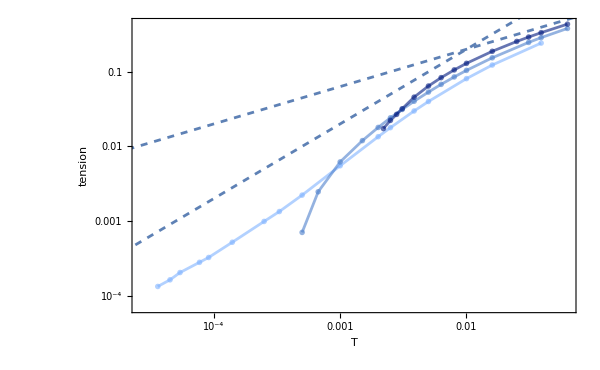

```mathematica
tensionPLot=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],tension[[p,T]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],PlotMarkers->pm1[9,blueGraient],ImageSize->600,Joined->True,FrameLabel->{"T","tension"},PlotStyle->blueGraient,PlotLegends->Table["p0="<>ToString[p0s[[p]]],{p,Length[p0s]}]],LogLogPlot[2x^0.5,{x,0.00001,0.1},PlotStyle->Dashed],LogLogPlot[20x,{x,0.00001,0.1},PlotStyle->Dashed]]
```

```mathematica
Export["/home/chengling/Research/updates/11102024/tension.jpeg",tensionPLot,ImageResolution->300]
```

/home/chengling/Research/updates/11102024/tension.jpeg

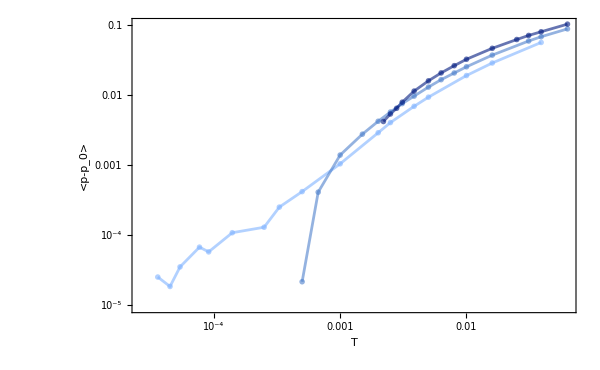

```mathematica
pminusp0Plot=ListLogLogPlot[Table[Table[{temperatures[[p,T]],meanPminusp0[[p,T]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],PlotMarkers->pm2[9,blueGraient],ImageSize->600,Joined->True,PlotStyle->blueGraient,FrameLabel->{"T","<p-p_0>"},PlotLegends->Table["p0="<>ToString[p0s[[p]]],{p,Length[p0s]}]]
```

```mathematica
Export["/home/chengling/Research/updates/11102024/pminusp0Plot.jpeg",pminusp0Plot,ImageResolution->300]
```

/home/chengling/Research/updates/11102024/pminusp0Plot.jpeg

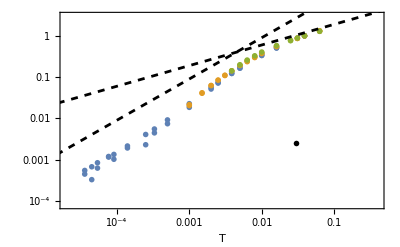

```mathematica
comparisionPlot=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],tension[[p,T]]/tension[[p,{1,2,2}[[p]]]]},{T,Length[temperatures[[p]]]-{0,2,4}[[p]]}],{p,Length[p0s]}],PlotMarkers->pm1[9,blueGraient],FrameLabel->{"T",None},PlotRange->{{0.00002,0.4},{0.00008,3}},LabelStyle->Directive[FontSize->24,FontName->"Arial"],Epilog->{Inset[pdfp,{-3.5,-6},Automatic]},ImageSize->400(*,PlotLegends->Table["tension: p0="<>ToString[p0s[[p]]],{p,Length[p0s]}]*),FrameTicks->{{{{0.00002,None,0.01},{0.00003,None,0.01},{0.00004,None,0.01},{0.00005,None,0.01},{0.00006,None,0.01},{0.00007,None,0.01},{0.00008,None,0.01},{0.00009,None,0.01},{0.0001,"10^-4",0.025},{0.0002,None,0.01},{0.0003,None,0.01},{0.0004,None,0.01},{0.0005,None,0.01},{0.0006,None,0.01},{0.0007,None,0.01},{0.0008,None,0.01},{0.0009,None,0.01},{0.001,"10^-3",0.025},{0.002,None,0.01},{0.003,None,0.01},{0.004,None,0.01},{0.005,None,0.01},{0.006,None,0.01},{0.007,None,0.01},{0.008,None,0.01},{0.009,None,0.01},{0.01,0.01,0.025},{0.02,None,0.01},{0.03,None,0.01},{0.04,None,0.01},{0.05,None,0.01},{0.06,None,0.01},{0.07,None,0.01},{0.08,None,0.01},{0.09,None,0.01},{0.1,0.1,0.025},{0.2,None,0.01},{0.3,None,0.01},{0.4,None,0.01},{0.5,None,0.01},{0.6,None,0.01},{0.7,None,0.01},{0.8,None,0.01},{0.9,None,0.01},{1,1,0.025},{2,None,0.01}},None},{{{0.00002,None,0.01},{0.00003,None,0.01},{0.00004,None,0.01},{0.00005,None,0.01},{0.00006,None,0.01},{0.00007,None,0.01},{0.00008,None,0.01},{0.00009,None,0.01},{0.0001,"10^-4",0.025},{0.0002,None,0.01},{0.0003,None,0.01},{0.0004,None,0.01},{0.0005,None,0.01},{0.0006,None,0.01},{0.0007,None,0.01},{0.0008,None,0.01},{0.0009,None,0.01},{0.001,"10^-3",0.025},{0.002,None,0.01},{0.003,None,0.01},{0.004,None,0.01},{0.005,None,0.01},{0.006,None,0.01},{0.007,None,0.01},{0.008,None,0.01},{0.009,None,0.01},{0.01,0.01,0.025},{0.02,None,0.01},{0.03,None,0.01},{0.04,None,0.01},{0.05,None,0.01},{0.06,None,0.01},{0.07,None,0.01},{0.08,None,0.01},{0.09,None,0.01},{0.1,0.1,0.025},{0.2,None,0.01},{0.3,None,0.01},{0.4,None,0.01},{0.5,None,0.01},{0.6,None,0.01},{0.7,None,0.01},{0.8,None,0.01},{0.9,None,0.01},{1,1,0.025},{2,None,0.01}},None}}],ListLogLogPlot[Table[Table[{temperatures[[p,T]],meanPminusp0[[p,T]]/meanPminusp0[[p,{1,2,2}[[p]]]]},{T,Length[temperatures[[p]]]-{0,2,4}[[p]]}],{p,Length[p0s]}](*,PlotLegends->Table["<p-p0>: p0="<>ToString[p0s[[p]]],{p,Length[p0s]}]*),PlotMarkers->pm2[9,blueGraient]](*,ListLogLogPlot[Table[Table[{temperatures[[p,T]],tension[[p,T]]/tension[[p,{1,2,2}[[p]]]]},{T,Length[temperatures[[p]]]-{8,1,3}[[p]],Length[temperatures[[p]]]}],{p,2,3}],PlotMarkers->pm1[9,blueGraient],PlotMarkers->{openHexagon,0.07},PlotLegends->Table["tension: p0="<>ToString[p0s[[p]]],{p,Length[p0s]}]],ListLogLogPlot[Table[Table[{temperatures[[p,T]],meanPminusp0[[p,T]]/meanPminusp0[[p,{1,2,2}[[p]]]]},{T,Length[temperatures[[p]]]-{8,1,3}[[p]],Length[temperatures[[p]]]}],{p,2,3}],PlotMarkers->{openHexagon,0.07},PlotLegends->Table["<p-p0>: p0="<>ToString[p0s[[p]]],{p,Length[p0s]}],PlotMarkers->pm2[9,blueGraient]]*),LogLogPlot[90x,{x,0.00001,0.1},PlotStyle->{Black,Dashed}],LogLogPlot[6x^0.5,{x,0.00001,0.6},PlotStyle->{Black,Dashed}]]
```

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/paperFigures/tension.jpeg",comparisionPlot,ImageResolution->300]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/paperFigures/tension.jpeg